### Generate Plot of N vs μ, ρ, and T_c

This notebook is used to generate the plot shown in Fig. 1 of Sridhar and Choueiri [1].

Dependencies:
The following dependencies are needed for evaluating this notebook:
1. MaTeX [2]
2. Graphics Information [3]

If not found, an attempt will be made to download and install them when this notebook is evaluated. If that fails, please download and install the dependencies manually before evaluating the notebook again.

References:
[1] R. Sridhar and E. Y. Choueiri, “Optimal Series Truncation of the Rigid-Sphere Head-Related Transfer Function for Accurate Binaural Perception,” J. Audio Eng. Soc., 2021 (to appear)
[2] S. Horvat, “MaTeX,” (2020 Oct), doi:10.5281/ zenodo.4116357, https://doi.org/10.5281/ zenodo.4116357
[3] C. Woll, “Graphics Information,” https://github.com/carlwoll/GraphicsInformation

License:
This file is part of the RS-HRTF Computation software.

Rahulram Sridhar <rahulram@princeton.edu>
3D Audio and Applied Acoustics (3D3A) Laboratory
Princeton University, Princeton, New Jersey 08544, USA

MIT License

Copyright (c) 2021 Rahulram Sridhar

Permission is hereby granted, free of charge, to any person obtaining a copy of this software and associated documentation files (the “Software”), to deal in the Software without restriction, including without limitation the rights to use, copy, modify, merge, publish, distribute, sublicense, and/or sell copies of the Software, and to permit persons to whom the Software is furnished to do so, subject to the following conditions:

The above copyright notice and this permission notice shall be included in all copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED “AS IS”, WITHOUT WARRANTY OF ANY KIND, EXPRESS OR IMPLIED, INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY, FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL THE AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM, DAMAGES OR OTHER LIABILITY, WHETHER IN AN ACTION OF CONTRACT, TORT OR OTHERWISE, ARISING FROM, OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE SOFTWARE.

#### Specify paths (do not modify this cell)

```mathematica
notebookDir=NotebookDirectory[];
splitDir=FileNameSplit[notebookDir];
splitPos=Position[splitDir,"Software"][[1,1]];
projectPath=FileNameJoin[splitDir[[1;;splitPos-1]]];
dataPath=FileNameJoin[{projectPath,"Data"}];
plotsPath=FileNameJoin[{projectPath,"Plots"}];
```

#### Install packages (do not modify this cell)

```mathematica
Needs["PacletManager`"]

If[Length[PacletFind["MaTeX"]]==0,
If[$VersionNumber≥11.3,
MessageDialog["Attempting to download and install MaTeX..."];
failFlag=Check[ResourceFunction["MaTeXInstall"][],True];
If[BooleanQ[failFlag],
MessageDialog["Unable to download and install MaTeX. Please do so manually. Aborting..."];
Abort[]
]
,
MessageDialog["MaTeX not installed. Please download and install manually. Aborting..."];
Abort[]
]
]
<<MaTeX`

If[Length[PacletFind["GraphicsInformation"]]==0,
MessageDialog["Attempting to download and install GraphicsInformation..."];
failFlag=Check[PacletInstall["GraphicsInformation","Site"->"http://raw.githubusercontent.com/carlwoll/GraphicsInformation/master"],True];
If[BooleanQ[failFlag],
MessageDialog["Unable to download and install GraphicsInformation. Please do so manually. Aborting..."];
Abort[]
]
]
<<GraphicsInformation`
```

#### Specify file to import

```mathematica
fileName="N_vs_mu_rho_and_Tc_plotdata";
```

#### Import data and prepare to generate plot

```mathematica
rawData=Import[FileNameJoin[{dataPath,"Plot Data",fileName<>".mat"}],"LabeledData"];
xData1="xData"/.rawData;
yData1="yData"/.rawData;
headRad=Flatten["a"/.rawData][[1]];
soundSpeed=Flatten["c"/.rawData][[1]];

numDataPts1=Dimensions[xData1][[1]];
numLines1=Dimensions[yData1][[2]];
linePlotData1=Table[{xData1[[ii,1]],yData1[[ii,jj]]},{jj,1,numLines1},{ii,1,numDataPts1}];
```

#### Generate basic (unformatted) plot

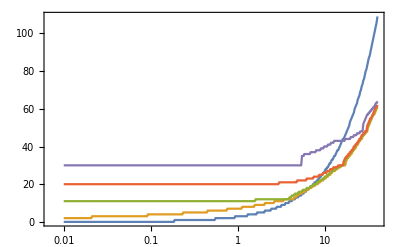

```mathematica
plot1=ListLogLinearPlot[linePlotData1,
Joined->True,
PlotRange->All
];

Show[plot1,
Axes->False,
Frame->True
]
```

#### Specify basic formatting variables

```mathematica
fontSize=10; (* Set equal to font size of document *)
baseStyle={FontFamily->"Times",FontSize->fontSize};
aspectRatio=3/4; (* Sets aspect ratio of the frame *)
columnWidth=234; (* Set equal to column width of document *)
pageWidth=486; (* Set equal to text width of document *)
plotLineThickness=0.006;
gridLineThickness=0.003;
SetOptions[MaTeX,FontSize->fontSize,ContentPadding->False,"Preamble"->{"\\usepackage{mathptmx}"}];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"];

majorTickLenY=0.015;
minorTickLenY=majorTickLenY 0.5;
majorTickLenX=majorTickLenY/aspectRatio;
minorTickLenX=minorTickLenY/aspectRatio;
```

#### Specify plot ticks and tick labels

```mathematica
xTickRange={0.008,40};
yTickRange={0,60};

bottomXMajorTicks={0.01,0.1,0.5,1,2,5,10,40};
bottomXAllTicks=Join[{0.008,0.009},Range[0.01,0.09,0.01],Range[0.1,0.9,0.1],Range[1,9],Range[10,40,10]];
bottomXMajorTickLabels=MaTeX[ToString/@bottomXMajorTicks];
numBottomXMajorTicks=Length[bottomXMajorTicks];

linFreqList={0.01,0.1,0.5,1,2,5,10,20};
topXMajorTicks=linFreqList 1000 2 π headRad/soundSpeed;
topXAllTicks=Join[Range[0.005,0.009,0.001],Range[0.01,0.09,0.01],Range[0.1,0.9,0.1],Range[1,9],{10,20,30}]1000 2 π headRad/soundSpeed;
topXMajorTickLabels=MaTeX[ToString/@linFreqList];
numTopXMajorTicks=Length[topXMajorTicks];

leftYMajorTicks=Range[0,60,15];
leftYAllTicks=Range[0,60,3];
leftYMajorTickLabels=MaTeX[ToString/@leftYMajorTicks];
numLeftYMajorTicks=Length[leftYMajorTicks];

rightYMajorTicks=leftYMajorTicks;
rightYAllTicks=leftYAllTicks;
numRightYMajorTicks=Length[rightYMajorTicks];
rightYMajorTickLabels=ConstantArray["",numRightYMajorTicks];
```

#### Compute additional plot ticks and tick labels

```mathematica
bottomXMinorTicks=Complement[bottomXAllTicks,bottomXMajorTicks];
topXMinorTicks=Complement[topXAllTicks,topXMajorTicks];
leftYMinorTicks=Complement[leftYAllTicks,leftYMajorTicks];
rightYMinorTicks=Complement[rightYAllTicks,rightYMajorTicks];

numBottomXMinorTicks=Length[bottomXMinorTicks];
numTopXMinorTicks=Length[topXMinorTicks];
numLeftYMinorTicks=Length[leftYMinorTicks];
numRightYMinorTicks=Length[rightYMinorTicks];

bottomXMinorTickLabels=ConstantArray["",numBottomXMinorTicks];
topXMinorTickLabels=ConstantArray["",numTopXMinorTicks];
leftYMinorTickLabels=ConstantArray["",numLeftYMinorTicks];
rightYMinorTickLabels=ConstantArray["",numRightYMinorTicks];

xPlotRange={0.007,57};
yPlotRange={-4,64};

leftTicks=Join[Table[{leftYMajorTicks[[ii]],leftYMajorTickLabels[[ii]],{majorTickLenY,0}},{ii,1,numLeftYMajorTicks}],Table[{leftYMinorTicks[[ii]],leftYMinorTickLabels[[ii]],{minorTickLenY,0}},{ii,1,numLeftYMinorTicks}]];
rightTicks=Join[Table[{rightYMajorTicks[[ii]],rightYMajorTickLabels[[ii]],{majorTickLenY,0}},{ii,1,numRightYMajorTicks}],Table[{rightYMinorTicks[[ii]],rightYMinorTickLabels[[ii]],{minorTickLenY,0}},{ii,1,numRightYMinorTicks}]];
bottomTicks=Join[Table[{Log[bottomXMajorTicks[[ii]]],bottomXMajorTickLabels[[ii]],{majorTickLenX,0}},{ii,1,numBottomXMajorTicks}],Table[{Log[bottomXMinorTicks[[ii]]],bottomXMinorTickLabels[[ii]],{minorTickLenX,0}},{ii,1,numBottomXMinorTicks}]];
topTicks=Join[Table[{Log[topXMajorTicks[[ii]]],topXMajorTickLabels[[ii]],{majorTickLenX,0}},{ii,1,numTopXMajorTicks}],Table[{Log[topXMinorTicks[[ii]]],topXMinorTickLabels[[ii]],{minorTickLenX,0}},{ii,1,numTopXMinorTicks}]];
```

#### Generate formatted plot

```mathematica
formattedPlot1=ListLogLinearPlot[linePlotData1,
Joined->True,
PlotStyle->Reverse[{{RGBColor[0.6,0.6,0.6],Thickness[plotLineThickness]},{RGBColor[0.4,0.4,0.4],Thickness[plotLineThickness]},{RGBColor[0.2,0.2,0.2],Thickness[plotLineThickness]},{RGBColor[0,0,0],Thickness[plotLineThickness]},{RGBColor[0,0,0],Thickness[plotLineThickness],Dashed}}],
PlotRange->{xPlotRange,yPlotRange}
];

formattedPlot=Show[formattedPlot1,
Axes->False,
Frame->True,
FrameTicks->{{leftTicks,rightTicks},{bottomTicks,topTicks}},
FrameTicksStyle->{{FontSize->fontSize,FontSize->0.1},{FontSize->fontSize,FontSize->fontSize}},
GridLines->{Join[Table[{Log[bottomXMajorTicks[[ii]]],Directive[LightGray,Thickness[gridLineThickness]]},{ii,1,numBottomXMajorTicks}],Table[{Log[bottomXMinorTicks[[jj]]],Directive[LightGray,Thickness[gridLineThickness/2]]},{jj,1,numBottomXMinorTicks}]],Table[{leftYMajorTicks[[kk]],Directive[LightGray,Thickness[gridLineThickness]]},{kk,1,numLeftYMajorTicks}]},
FrameStyle->Directive[Black,Thickness[gridLineThickness]],
FrameLabel->{{MaTeX["\\textrm{Truncation order},~N"],None},{MaTeX["\\textrm{Non-dimensional frequency},~\\mu"],MaTeX["\\textrm{Frequency},~f~(\\textrm{kHz})"]}},
BaseStyle->baseStyle,
ImageSize->columnWidth,
ImagePadding->{{42.87,42.87},{All,All}}, (* Final setting *)
(*ImagePadding->All,*) (* Initial setting *)
AspectRatio->aspectRatio,
Epilog->{Text[MaTeX["\\rho = 3/2"],{Log[0.03],34}],Text[MaTeX["2"],{Log[0.03],23}],Text[MaTeX["3"],{Log[0.05],14}],Text[MaTeX["\\rho \\to \\infty"],{Log[0.15],6.5}],Text[MaTeX["\\textrm{Eq.}~(13)"],{Log[7],3}]}
];

(* Check values of ImagePadding when it is set to All and then adjust values accordingly *)
graphicsInfo=GraphicsInformation[formattedPlot];
imagePadding="ImagePadding"/.graphicsInfo;
Print["{{Left,Right},{Bottom,Top}}: "<>ToString[imagePadding]]
```

{{Left,Right},{Bottom,Top}}: {{42.87, 42.87}, {31., 29.9512}}

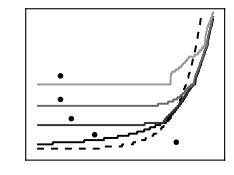

```mathematica
Magnify[formattedPlot,2]
```

#### Specify plot export settings

```mathematica
(* Do NOT include file extension in plotDataFileName *)
plotDataFileName="N_vs_mu_rho_and_Tc_grayscale";
(* Options for fileType: "EPS" and "PDF" *)
fileType="PDF";
```

#### Export plot (do not modify this cell)

Note: When EPS export doesn’t render properly, export as PDF and then convert to EPS externally (e.g., using “pdftops”).

```mathematica
fileType=ToUpperCase[fileType];
Switch[fileType,
"EPS",
plotFilePath=FileNameJoin[{plotsPath,"Computation",plotDataFileName<>".eps"}];
Export[plotFilePath,formattedPlot,fileType,Background->None,ImageResolution->600];
,"PDF",
plotFilePath=FileNameJoin[{plotsPath,"Computation",plotDataFileName<>".pdf"}];
Export[plotFilePath,formattedPlot,fileType,Background->None];
,_,
fileType="PDF";
plotFilePath=FileNameJoin[{plotsPath,"Computation",plotDataFileName<>".pdf"}];
Export[plotFilePath,formattedPlot,fileType,Background->None];
]
```

#### (Optional) Export padding values as text file (do not modify this cell)

```mathematica
txtFilePath=FileNameJoin[{plotsPath,"Computation",plotDataFileName<>"_padding.txt"}];
Export[txtFilePath,{{"Left","Right","Bottom","Top","(pts)"},Flatten[Round[imagePadding,0.1]]},"Table","FieldSeparators"->" "];
```